```mathematica
DateString[]
<<SymbolicComputing`
$Version
$SCVersion
```

Tue 9 Jan 2018 00:11:03

11.2.0 for Linux x86 (64-bit) (September 11, 2017)

4.0.0 (September 4, 2016)

## At Day 9

[1] C. Arangala and K. A. Yokley, Exploring Calculus: Labs and Projects with Mathematica, 1st ed. Chapman and Hall/CRC, 2016.

-Graphics-

## 3 Areas, Integrals, and Accumulation

## Lab 19: Summation

```mathematica
SCAFE[∑_(i=1)^n 6,SCEvalSum]
```

∑_(i=1)^n 6==6 n

SCSumChangeInterval changes the interval of summation. The validity of equation is up to the user.

```mathematica
SCAFE[∑_(i=1)^n 6,SCSumChangeInterval,{All,{i,0,n-1}},$,Apply->SCEvalSum]
```

∑_(i=1)^n 6==6 ∑_(i=0)^(-1+n) 1

SCSumChangeLimits changes the interval of summation and keeps the validity of the equation.

```mathematica
SCAFE[∑_(i=1)^n 6,SCSumChangeLimits,{All,{i,0,n-1}},$,Apply->SCEvalSum]
```

∑_(i=1)^n 6==6 ∑_(i=0)^(-1+n) 1

Gauss’ sum trick

```mathematica
Grid@{Range[10],Reverse@Range[10],Range[10]+Reverse@Range[10]}
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
10 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 1
11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11

```mathematica
SCAFE[∑_(i=1)^n i,SCEvalSum]
```

∑_(i=1)^n i==1/2 n (1+n)

Derivation of an equation for the sum of squared natural numbers.

```mathematica
∑_(i=1)^n i^2==a n^3+b n^2+c n+d
SCMAF[%,Table[#/.n->l,{l,4}]&,All,Apply->SCEvalSum,
SCSolve,{All,{a,b,c,d}}]
```

∑_(i=1)^n i^2==d+c n+b n^2+a n^3

{1==a+b+c+d,5==8 a+4 b+2 c+d,14==27 a+9 b+3 c+d,30==64 a+16 b+4 c+d}

{a==1/3,b==1/2,c==1/6,d==0}

```mathematica
∑_(i=1)^n i^2==a n^3+b n^2+c n+d
SCMAF[%,RA,{At[2],{a==1/3,b==1/2,c==1/6,d==0}},Apply->Factor]
```

∑_(i=1)^n i^2==d+c n+b n^2+a n^3

∑_(i=1)^n i^2==1/6 n (1+n) (1+2 n)

```mathematica
SCAFE[∑_(i=1)^n i^2,SCEvalSum]
```

∑_(i=1)^n i^2==1/6 n (1+n) (1+2 n)

Derivation of an equation for the sum of cubed natural numbers.

```mathematica
∑_(i=1)^n i^3==a n^4+b n^3+c n^2+d n+e
SCMAF[%,Table[#/.n->l,{l,5}]&,All,Apply->SCEvalSum,
SCSolve,{All,{a,b,c,d,e}}]
```

∑_(i=1)^n i^3==e+d n+c n^2+b n^3+a n^4

{1==a+b+c+d+e,9==16 a+8 b+4 c+2 d+e,36==81 a+27 b+9 c+3 d+e,100==256 a+64 b+16 c+4 d+e,225==625 a+125 b+25 c+5 d+e}

{a==1/4,b==1/2,c==1/4,d==0,e==0}

```mathematica
∑_(i=1)^n i^3==a n^4+b n^3+c n^2+d n+e
SCMAF[%,RA,{At[2],{a==1/4,b==1/2,c==1/4,d==0,e==0}},Apply->Factor]
```

∑_(i=1)^n i^3==e+d n+c n^2+b n^3+a n^4

∑_(i=1)^n i^3==1/4 n^2 (1+n)^2

```mathematica
SCAFE[∑_(i=1)^n i^3,SCEvalSum]
```

∑_(i=1)^n i^3==1/4 n^2 (1+n)^2

## Lab 20: Riemann Sums

Demonstration: Riemann Sums

```mathematica
{Subscript[L, n]==∑_(i=0)^(n-1) (b-a)/n f[a+(i(b-a))/n],Subscript[R, n]==Subscript[L, n]==∑_(i=1)^n (-a+b)/n (-1+(a+((-a+b) i)/n)^3)}
SCMAF[%,RA,{All,f[x_]->x^3-1}]
```

{L_n==∑_(i=0)^(-1+n) (-a+b)/n f[a+((-a+b) i)/n],R_n==L_n==∑_(i=1)^n (-a+b)/n (-1+(a+((-a+b) i)/n)^3)}

{L_n==∑_(i=0)^(-1+n) (-a+b)/n (-1+(a+((-a+b) i)/n)^3),R_n==L_n==∑_(i=1)^n (-a+b)/n (-1+(a+((-a+b) i)/n)^3)}

```mathematica
Table[Subscript[L, n]==∑_(i=0)^(-1+n) (-a+b)/n (-1+(a+((-a+b) i)/n)^3),{n,{4,10,100}}]
SCMAF[%,RA,{All,{a==1,b==4}},
SCEvalSum,All,Apply->N]
```

{L_4==∑_(i=0)^3 1/4 (-a+b) (-1+(a+1/4 (-a+b) i)^3),L_10==∑_(i=0)^9 1/10 (-a+b) (-1+(a+1/10 (-a+b) i)^3),L_100==∑_(i=0)^99 1/100 (-a+b) (-1+(a+1/100 (-a+b) i)^3)}

{L_4==3/4 ∑_(i=0)^3 (-1+(1+(3 i)/4)^3),L_10==3/10 ∑_(i=0)^9 (-1+(1+(3 i)/10)^3),L_100==3/100 ∑_(i=0)^99 (-1+(1+(3 i)/100)^3)}

{L_4==39.2344,L_10==51.6375,L_100==59.8084}

```mathematica
SCAFE[∫_1^4 (x^3-1)ⅆx,SCEvalInt,Apply->N]
```

∫_1^4 (-1+x^3)ⅆx==60.75

```mathematica
SCARA[Underscript[Limit, n->∞][Subscript[L, n]],Subscript[L, n]==∑_(i=0)^(-1+n) (-a+b)/n (-1+(a+((-a+b) i)/n)^3)]
SCMAF[%,SCEvalSum,At[2],Apply->SCEvalLimit]
```

Limit_(n→∞)[L_n]==Limit_(n→∞)[∑_(i=0)^(-1+n) (-a+b)/n (-1+(a+((-a+b) i)/n)^3)]

Limit_(n→∞)[L_n]==1/4 (4 a-a^4-4 b+b^4)

```mathematica
SCARA[Underscript[Limit, n->∞][Subscript[R, n]],Subscript[R, n]==∑_(i=1)^n (-a+b)/n (-1+(a+((-a+b) i)/n)^3)]
SCMAF[%,SCEvalSum,At[2],Apply->SCEvalLimit]
```

Limit_(n→∞)[R_n]==Limit_(n→∞)[∑_(i=1)^n (-a+b)/n (-1+(a+((-a+b) i)/n)^3)]

Limit_(n→∞)[R_n]==1/4 (4 a-a^4-4 b+b^4)

```mathematica
Underscript[Limit, n->∞][Subscript[L, n]]==1/4 (4 a-a^4-4 b+b^4)/.{a->1,b->4}//N
```

Limit_(n→∞)[L_n]==60.75

## Lab 21: The Definite and Indefinite Integral

Indefinite integrals

f[x]==-1+x

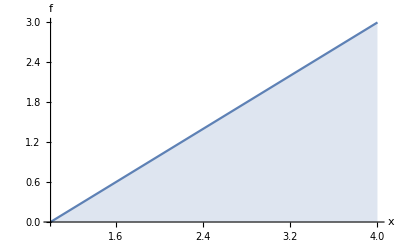

```mathematica
f[x]==x-1
SCMAF[%,Plot,{At[2],{x,1,4},AxesLabel->{x,f},{Filling->Axis}},Take->{2}]
```

```mathematica
SCAFE[∫_1^4 (x-1)ⅆx,SCEvalInt]
```

∫_1^4 (-1+x)ⅆx==9/2

f[x]==-1+x

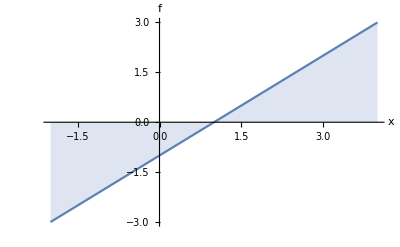

```mathematica
f[x]==x-1
SCMAF[%,Plot,{At[2],{x,-2,4},AxesLabel->{x,f},{Filling->Axis}},Take->{2}]
```

```mathematica
SCAFE[∫_-2^4 (x-1)ⅆx,SCEvalInt]
```

∫_-2^4 (-1+x)ⅆx==0

f[x]==Sin[x]

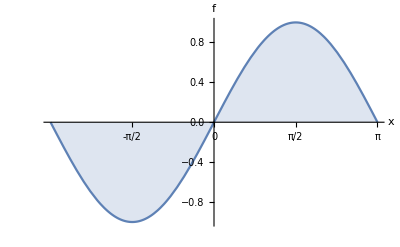

```mathematica
f[x]==Sin[x]
SCMAF[%,Plot,{At[2],{x,-π,π},Ticks->{-π/2+π/2 Range[0,4],Automatic},AxesLabel->{x,f},{Filling->Axis}},Take->{2}]
```

```mathematica
SCAFE[∫_-π^π Sin[x]ⅆx,SCEvalInt]
```

∫_-π^π Sin[x]ⅆx==0

Definite integrals

```mathematica
SCAFE[∫2xⅆx,SCEvalInt,{All,ReplConst->C}]
```

∫2 xⅆx==C+x^2

Fundamental Theorem of Calculus - Part I

If f(x) is a continuous function on the interval [a,b] and F(x) is the indefinite integral of f(x) on [a,b], then ∫_a^b f(x)ⅆx=F(b)-F(a).

```mathematica
∫_1^3 2xⅆx==F[3]-F[1]
SCMAF[%,RA,{At[2],F[x_]==x^2+C},ApplyAll->SCEvalInt]
```

∫_1^3 2 xⅆx==-F[1]+F[3]

True

## Lab 22: Basic Integration Techniques

```mathematica
SCAFE[∫x^n ⅆx,SCEvalInt,{All,ReplConst->C}]
```

∫x^n ⅆx==C+x^(1+n)/(1+n)

The antiderivative is a linear operator.

```mathematica
SCAFE[∫k f[x]ⅆx,SCFactorInt,{All,k}]
```

∫k f[x]ⅆx==k ∫f[x]ⅆx

```mathematica
SCAFE[∫(f[x]+g[x])ⅆx,SCExpandInt,All]
```

∫(f[x]+g[x])ⅆx==∫f[x]ⅆx+∫g[x]ⅆx

```mathematica
SCAFE[∫4xⅆx,SCFactorInt,Apply->SCEvalInt]
```

∫4 xⅆx==2 x^2

```mathematica
SCAFE[∫(4x-16 x^3)ⅆx,SCExpandInt,Apply->SCEvalInt]
```

∫(4 x-16 x^3)ⅆx==2 x^2-4 x^4

```mathematica
SCAFE[∫_0^(1/2) (4x-16 x^3)ⅆx,SCExpandInt,Apply->SCEvalInt]
```

∫_0^(1/2) (4 x-16 x^3)ⅆx==1/4

Indefinite integral of non-polynomial functions

```mathematica
SCAFE[∫Cos[x]ⅆx,SCEvalInt]
```

∫Cos[x]ⅆx==Sin[x]

```mathematica
SCAFE[∫Sin[x]ⅆx,SCEvalInt]
```

∫Sin[x]ⅆx==-Cos[x]

```mathematica
SCAFE[∫Sec[x]^2 ⅆx,SCEvalInt]
```

∫Sec[x]^2 ⅆx==Tan[x]

```mathematica
SCAFE[∫Sec[x]Tan[x]ⅆx,SCEvalInt]
```

∫Sec[x] Tan[x]ⅆx==Sec[x]

```mathematica
SCAFE[∫ⅇ^x ⅆx,SCEvalInt]
```

∫ⅇ^x ⅆx==ⅇ^x

## Lab 23: Fundamental Theorem of Calculus - Part II

Based on FTC,

```mathematica
∫_a_^b_ f_ⅆx:>Subscript[Integrate[f,x], x==b]-Subscript[Integrate[f,x], x==a]
```

∫_a_^b_ f_ⅆx:>(∫fⅆx)_(x==b)-(∫fⅆx)_(x==a)

```mathematica
SCARA[{∫_0^1 x^3 ⅆx,∫_1^2 x^3 ⅆx,∫_0^2 x^3 ⅆx},∫_a_^b_ f_ⅆx_:>Subscript[Integrate[f,x], x==b]-Subscript[Integrate[f,x], x==a]]
SCMAF[%,Thread,All,Apply->SCEvalEqSub]
```

{∫_0^1 x^3 ⅆx,∫_1^2 x^3 ⅆx,∫_0^2 x^3 ⅆx}=={-(x^4/4)_(x==0)+(x^4/4)_(x==1),-(x^4/4)_(x==1)+(x^4/4)_(x==2),-(x^4/4)_(x==0)+(x^4/4)_(x==2)}

{∫_0^1 x^3 ⅆx==1/4,∫_1^2 x^3 ⅆx==15/4,∫_0^2 x^3 ⅆx==4}

```mathematica
SCARA[∫_a^b f[x]ⅆx+∫_b^c f[x]ⅆx,∫_a_^b_ f_ⅆx:>Subscript[Integrate[f,x], x==b]-Subscript[Integrate[f,x], x==a]]
SCMAF[%,RA,{All,Subscript[Integrate[f_,x_], x_==b_]-Subscript[Integrate[f_,x_], x_==a_]:>∫_a^b fⅆx}]
```

∫_a^b f[x]ⅆx+∫_b^c f[x]ⅆx==-(∫f[x]ⅆx)_(x==a)+(∫f[x]ⅆx)_(x==c)

∫_a^b f[x]ⅆx+∫_b^c f[x]ⅆx==∫_a^c f[x]ⅆx

FTC - Part II states that if f(x) is a continuous function on [a,b], then ⅆ/ⅆx(∫_a^x f(t)ⅆt)=f(x) where x∈[a,b].

```mathematica
SCARA[ⅆg[x]/ⅆx,g[x]==∫_0^x Cos[t]ⅆt]
SCMAF[%,SCEvalInt,At[2],Apply->SCEvalDeriv]
```

ⅆg[x]/ⅆx==ⅆ/ⅆx∫_0^x Cos[t]ⅆt

ⅆg[x]/ⅆx==Cos[x]

```mathematica
SCARA[ⅆg[x]/ⅆx,g[x]==∫_0^(x^2) Cos[t]ⅆt]
SCMAF[%,SCEvalInt,At[2],Apply->SCEvalDeriv]
```

ⅆg[x]/ⅆx==ⅆ/ⅆx∫_0^(x^2) Cos[t]ⅆt

ⅆg[x]/ⅆx==2 x Cos[x^2]

```mathematica
SCARA[ⅆg[x]/ⅆx,g[x]==∫_0^Sin[x] Cos[t]ⅆt]
SCMAF[%,SCEvalInt,At[2],Apply->SCEvalDeriv]
```

ⅆg[x]/ⅆx==ⅆ/ⅆx∫_0^Sin[x] Cos[t]ⅆt

ⅆg[x]/ⅆx==Cos[x] Cos[Sin[x]]

```mathematica
SCARA[ⅆg[x]/ⅆx,g[x]==∫_(x^2)^(x^3) Cos[t]ⅆt]
SCMAF[%,SCEvalInt,At[2],Apply->SCEvalDeriv]
```

ⅆg[x]/ⅆx==ⅆ/ⅆx∫_(x^2)^(x^3) Cos[t]ⅆt

ⅆg[x]/ⅆx==-2 x Cos[x^2]+3 x^2 Cos[x^3]

```mathematica
D[Integrate[Cos[2t]/(√(t+1)),{t,1,x}],x]//Refine[#,x≥1]&//Simplify
```

Cos[2 x]/(√(1+x))

```mathematica
SCAFE[ⅆ/ⅆx∫_1^x Cos[2t]/(√(t+1))ⅆt,SCEvalInt]
SCMAF[%,Refine,{At[2],x≥1},
SCEvalDeriv,At[2],Apply->Simplify]
```

ⅆ/ⅆx∫_1^x Cos[2 t]/(√(1+t))ⅆt==ⅆ/ⅆx ConditionalExpression[√π (-Cos[2] FresnelC[2 √(2/π)]+Cos[2] FresnelC[(2 √(1+x))/(√π)]-FresnelS[2 √(2/π)] Sin[2]+Sin[2] FresnelS[(2 √(1+x))/(√π)]),Re[x]>-1||x∉ℝ]

ⅆ/ⅆx∫_1^x Cos[2 t]/(√(1+t))ⅆt==√π ⅆ/ⅆx(-Cos[2] FresnelC[2 √(2/π)]+Cos[2] FresnelC[(2 √(1+x))/(√π)]-FresnelS[2 √(2/π)] Sin[2]+Sin[2] FresnelS[(2 √(1+x))/(√π)])

ⅆ/ⅆx∫_1^x Cos[2 t]/(√(1+t))ⅆt==Cos[2 x]/(√(1+x))

## Lab 24: Substitution and Parts

Substitution with indefinite integrals

```mathematica
SCAFE[∫Sin[2x]ⅆx,SCEvalInt,{All,ReplConst->C}]
```

∫Sin[2 x]ⅆx==C-1/2 Cos[2 x]

```mathematica
SCAFE[∫Sin[2x]ⅆx,SCTransInt,{All,TransVar->{x,u,2x==u}}]
SCMAF[%,SCEvalInt,{At[2],ReplConst->C},
RA,{At[2],u==2x}]
```

∫Sin[2 x]ⅆx==1/2 ∫Sin[u]ⅆu

∫Sin[2 x]ⅆx==1/2 (C-Cos[u])

∫Sin[2 x]ⅆx==1/2 (C-Cos[2 x])

```mathematica
SCAFE[∫3 x^2 √(4 x^3+6)ⅆx,SCTransInt,{All,TransVar->{x,u,4 x^3+6==u}}]
SCMAF[%,SCEvalInt,{At[2],ReplConst->4C},
RA,{At[2],u==4 x^3+6},ExpandAll,At[2],Apply->Simplify]
```

∫3 x^2 √(6+4 x^3)ⅆx==1/4 ∫√u ⅆu

3 ∫x^2 √(6+4 x^3)ⅆx==1/4 (4 C+2/3 (6+4 x^3)^(3/2))

3 ∫x^2 √(6+4 x^3)ⅆx==C+1/3 √2 (3+2 x^3)^(3/2)

```mathematica
SCAFE[∫(4x)/(√(x^2+6))ⅆx,SCTransInt,{All,TransVar->{x,u,6+x^2==u}}]
SCMAF[%,SCEvalInt,{At[2],ReplConst->C/2},
RA,{At[2],u==6+x^2},Apply->Simplify]
```

∫(4 x)/(√(6+x^2))ⅆx==2 ∫1/(√u)ⅆu

4 ∫x/(√(6+x^2))ⅆx==2 (C/2+2 √u)

4 ∫x/(√(6+x^2))ⅆx==C+4 √(6+x^2)

```mathematica
SCAFE[∫Sin[x]Cos[x]ⅆx,SCTransInt,{All,TransVar->{x,u,Sin[x]==u}}]
SCMAF[%,SCEvalInt,{At[2],ReplConst->C},
RA,{At[2],u==Sin[x]}]
```

∫Cos[x] Sin[x]ⅆx==∫uⅆu

∫Cos[x] Sin[x]ⅆx==C+u^2/2

∫Cos[x] Sin[x]ⅆx==C+Sin[x]^2/2

```mathematica
SCAFE[∫Sin[x]Cos[x]ⅆx,SCTransInt,{All,TransVar->{x,u,Cos[x]==u}}]
SCMAF[%,SCEvalInt,{At[2],ReplConst->-C},
RA,{At[2],u==Cos[x]}]
```

∫Cos[x] Sin[x]ⅆx==-∫uⅆu

∫Cos[x] Sin[x]ⅆx==C-u^2/2

∫Cos[x] Sin[x]ⅆx==C-Cos[x]^2/2

This result looks different from the above result.

```mathematica
∫Cos[x] Sin[x]ⅆx==C-Cos[x]^2/2
SCMAF[%,SCEliminate,{At[2],Cos[x]^2+Sin[x]^2==1,Cos[x]^2},Apply->Expand,
RA,{At[2],-1/2+C->C}]
```

∫Cos[x] Sin[x]ⅆx==C-Cos[x]^2/2

∫Cos[x] Sin[x]ⅆx==-1/2+C+Sin[x]^2/2

∫Cos[x] Sin[x]ⅆx==C+Sin[x]^2/2

```mathematica
SCAFE[∫Sec[x]Tan[x]ⅆx,SCTransInt,{All,TransVar->{x,u,Sec[x]==u}}]
SCMAF[%,SCEvalInt,{At[2],ReplConst->C},
RA,{At[2],u==Sec[x]}]
```

∫Sec[x] Tan[x]ⅆx==∫1ⅆu

∫Sec[x] Tan[x]ⅆx==C+u

∫Sec[x] Tan[x]ⅆx==C+Sec[x]

Definite integrals,

```mathematica
SCAFE[∫_-1^1 3 x^2 √(4 x^3+6)ⅆx,SCTransInt,{All,TransVar->{x,u,4 x^3+6==u}},Apply->SCEvalInt]
```

∫_-1^1 3 x^2 √(6+4 x^3)ⅆx==1/3 √2 (-1+5 √5)

```mathematica
SCAFE[∫_0^π Sin[x]Cos[x]ⅆx,SCTransInt,{All,TransVar->{x,u,Cos[x]==u}},Apply->SCEvalInt]
```

∫_0^π Cos[x] Sin[x]ⅆx==0

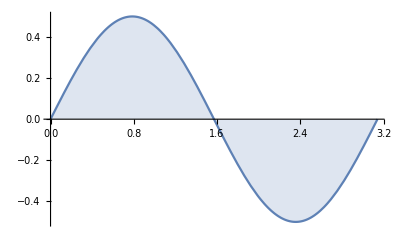

```mathematica
Plot[Sin[x]Cos[x],{x,0,π},Filling->Axis]
```

```mathematica
SCAFE[∫_0^π x Cos[x^2]ⅆx,SCTransInt,{All,TransVar->{x,u,Cos[x^2]==u}},Apply->SCEvalInt]
```

∫_0^π x Cos[x^2]ⅆx==-1/2 Sin[π^2]

Integration by parts

```mathematica
SCAFE[∫u[x]v'[x]ⅆx,SCIntByParts,{All,v'[x]}]
```

∫u[x] v'[x]ⅆx==-∫v[x] u'[x]ⅆx+u[x] v[x]

```mathematica
SCAFE[∫x ⅇ^x ⅆx,SCIntByParts,{All,ⅇ^x}]
SCMAF[%,SCEvalInt,{At[2],ReplConst->-C}]
```

∫ⅇ^x xⅆx==ⅇ^x x-∫ⅇ^x ⅆx

∫ⅇ^x xⅆx==C-ⅇ^x+ⅇ^x x

```mathematica
SCAFE[∫x Sin[x]ⅆx,SCIntByParts,{All,Sin[x]}]
SCMAF[%,SCEvalInt,{At[2],ReplConst->C}]
```

∫x Sin[x]ⅆx==-x Cos[x]+∫Cos[x]ⅆx

∫x Sin[x]ⅆx==C-x Cos[x]+Sin[x]

```mathematica
SCAFE[∫x Cos[x]ⅆx,SCIntByParts,{All,Cos[x]}]
SCMAF[%,SCEvalInt,{At[2],ReplConst->-C}]
```

∫x Cos[x]ⅆx==-∫Sin[x]ⅆx+x Sin[x]

∫x Cos[x]ⅆx==C+Cos[x]+x Sin[x]

```mathematica
SCAFE[∫x^2 ⅇ^x ⅆx,SCIntByParts,{All,ⅇ^x}]
SCMAF[%,SCIntByParts,{At[2],ⅇ^x},Apply->Expand,
SCEvalInt,{At[2],ReplConst->C/2},Apply->Simplify]
```

∫ⅇ^x x^2ⅆx==ⅇ^x x^2-2 ∫ⅇ^x xⅆx

∫ⅇ^x x^2ⅆx==-2 ⅇ^x x+ⅇ^x x^2+2 ∫ⅇ^x ⅆx

∫ⅇ^x x^2ⅆx==C+ⅇ^x (2-2 x+x^2)

```mathematica
SCAFE[ⅆ/ⅆx∫u[x]v'[x]ⅆx,SCIntByParts,{All,v'[x]},Apply->SCDerivExpand]
SCMAF[%,SCExpandInt,At[2],
SCIntByPartsDeriv,{∫v[x] (ⅆ^2 u[x])/(ⅆ x^2)ⅆx},
SCRestoreDeriv,At[2]]
```

ⅆ/ⅆx∫u[x] v'[x]ⅆx==-∫(ⅆu[x]/ⅆx ⅆv[x]/ⅆx+v[x] (ⅆ^2 u[x])/(ⅆ x^2))ⅆx+u[x] ⅆv[x]/ⅆx+v[x] ⅆu[x]/ⅆx

ⅆ/ⅆx∫u[x] v'[x]ⅆx==u[x] ⅆv[x]/ⅆx

ⅆ/ⅆx∫u[x] v'[x]ⅆx==u[x] v'[x]

## Lab 25: Introduction to Logarithmic Functions

The context does not show how to integrate log function.

```mathematica
SCAFE[∫Log[x]ⅆx,SCTransInt,{All,TransVar->{x,u,Log[x]==u}}]
SCMAF[%,Refine,{At[2],u∈Reals},
SCEvalInt,{At[2],ReplConst->C},Apply->ExpandAll,
RA,{At[2],u==Log[x]}]
```

∫Log[x]ⅆx==∫ConditionalExpression[ⅇ^u Log[ⅇ^u],-π<Im[u]≤π]ⅆu

∫Log[x]ⅆx==C-ⅇ^u+ⅇ^u u

∫Log[x]ⅆx==C-x+x Log[x]

Introduction

For general n, (n≠-1)

```mathematica
SCAFE[∫x^n ⅆx,SCEvalInt,{All,ReplConst->C}]
```

∫x^n ⅆx==C+x^(1+n)/(1+n)

```mathematica
SCAFE[∫x^-1 ⅆx,SCEvalInt,{All,ReplConst->C}]
```

∫1/x ⅆx==C+Log[x]

Exercises

```mathematica
ⅆP/ⅆt==r P
SCMAF[%,SCDerivToFrac,At[1],
SCMultEq,{All,ⅆt/P},Apply->SCDiffToInt,
SCEvalInt,{All,ReplConst->C},
SCSubtFromEq,{All,C},
RA,{At[2],-C+C[2]->C}]
```

ⅆP/ⅆt==P r

Log[P]==-C+r t+C[2]

Log[P]==C+r t

```mathematica
Log[P]==C+r t
SCMAF[%,SCSolve,{All,P,Reals}]
```

Log[P]==C+r t

P==ⅇ^(C+r t)

```mathematica
P==ⅇ^(C+r t)
SCMAF[%,RA,{All,{P==Subscript[P, 0],t==0}},
SCSolve,{All,C,Reals},
Refine,{All,Subscript[P, 0]>0}]
```

P==ⅇ^(C+r t)

ConditionalExpression[C==Log[P_0],P_0>0]

C==Log[P_0]

```mathematica
P==ⅇ^(C+r t)/.C->Log[Subscript[P, 0]]
```

P==ⅇ^(r t) P_0

The functions ⅇ^x and ln(x) are inverse functions.

```mathematica
SCAFE[HoldForm@(ⅇ^Log[x]),ReleaseHold]
```

ⅇ^Log[x]==x

```mathematica
SCAFE[Log[ⅇ^x],FullSimplify,{All,x∈Reals}]
```

Log[ⅇ^x]==x

Some additional properties of these functions are

```mathematica
SCAFE[HoldForm@(ⅇ^x)ⅇ^y,ReleaseHold]
```

ⅇ^y ⅇ^x==ⅇ^(x+y)

```mathematica
SCAFE[HoldForm@(ⅇ^x/ⅇ^y),ReleaseHold]
```

ⅇ^x/ⅇ^y==ⅇ^(x-y)

```mathematica
SCAFE[Log[x y],PowerExpand]
```

Log[x y]==Log[x]+Log[y]

```mathematica
{Log[x y],Log[x]+Log[y]}/.{x->-1,y->-1}
```

{0,2 ⅈ π}

```mathematica
SCAFE[Log[x/y],PowerExpand]
```

Log[x/y]==Log[x]-Log[y]

```mathematica
SCAFE[Log[x^p],PowerExpand]
```

Log[x^p]==p Log[x]

```mathematica
{Log[x^p],p Log[x]}/.{x->-1,p->-1}
```

{ⅈ π,-ⅈ π}

Derivatives and Antiderivatives Involving Logarithms

```mathematica
SCAFE[ⅆ/ⅆx Log[x],SCEvalDeriv]
```

ⅆLog[x]/ⅆx==1/x

```mathematica
SCAFE[ⅆ/ⅆx Log[x],SCEliminate,{All,Log[x]+C==∫1/x ⅆx,Log[x]}]
SCMAF[%,SCDerivExpand,{At[2]},Apply->SCEvalInt]
```

ⅆLog[x]/ⅆx==ⅆ/ⅆx(-C+∫1/x ⅆx)

ⅆLog[x]/ⅆx==1/x

```mathematica
SCAFE[ⅆ/ⅆx Log[x],SCEliminate,{All,Log[x]+C==∫1/x ⅆx,Log[x]}]
SCMAF[%,SCExpandDeriv,{At[2]},Apply->SCEvalInt,
SCEvalDeriv,{At[2]}]
```

ⅆLog[x]/ⅆx==ⅆ/ⅆx(-C+∫1/x ⅆx)

ⅆLog[x]/ⅆx==-ⅆC/ⅆx+ⅆLog[x]/ⅆx

ⅆLog[x]/ⅆx==1/x

```mathematica
SCAFE[ⅆ/ⅆx Log[b,x],SCEvalDeriv]
```

ⅆ/ⅆx Log[x]/Log[b]==1/(x Log[b])

```mathematica
SCAFE[∫x Log[x^2]ⅆx,SCEvalInt,{All,ReplConst->C},Apply->Simplify]
```

∫x Log[x^2]ⅆx==C-x^2/2+1/2 x^2 Log[x^2]

Using substitution,

```mathematica
SCAFE[∫x Log[x^2]ⅆx,SCTransInt,{All,TransVar->{x,u,x^2==u}}]
SCMAF[%,SCEvalInt,{At[2],ReplConst->2C},
RA,{At[2],u==x^2},Apply->Simplify]
```

∫x Log[x^2]ⅆx==1/2 ∫Log[u]ⅆu

∫x Log[x^2]ⅆx==1/2 (2 C-u+u Log[u])

∫x Log[x^2]ⅆx==C-x^2/2+1/2 x^2 Log[x^2]

Using integration by parts,

```mathematica
SCAFE[∫x Log[x^2]ⅆx,SCIntByParts,{All,x}]
SCMAF[%,SCEvalInt,{At[2],ReplConst->-C}]
```

∫x Log[x^2]ⅆx==1/2 x^2 Log[x^2]-∫xⅆx

∫x Log[x^2]ⅆx==C-x^2/2+1/2 x^2 Log[x^2]

## Lab 26: Inverse Trigonometric Functions and Trigonometric Substitution

The Inverse to cos(x)

```mathematica
{ArcCos[1],ArcCos[-1]}
```

{0,π}

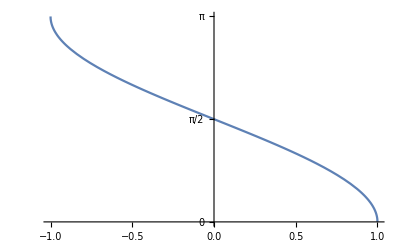

```mathematica
Plot[ArcCos[x],{x,-1,1},Ticks->{Automatic,{0,π/2,π}}]
```

```mathematica
SCAFE[HoldForm@(Sin[ArcCos[x]]^2),ReleaseHold]
```

Sin[ArcCos[x]]^2==1-x^2

```mathematica
Sin[arccos[x]]^2==1-x^2
SCMAF[%,(ⅆ#)/ⅆx&,All,Level->{1},Apply->SCEvalDeriv,
SCSolve,{All,arccos'[x]},
RA,{At[2],arccos[x]->ArcCos[x]}]
```

Sin[arccos[x]]^2==1-x^2

arccos'[x]==-x Csc[arccos[x]] Sec[arccos[x]]

arccos'[x]==-1/(√(1-x^2))

```mathematica
SCAFE[ⅆArcCos[x]/ⅆx,SCEvalDeriv,All,Apply->Simplify]
```

ⅆArcCos[x]/ⅆx==-1/(√(1-x^2))

The Inverse to sin(x) and tan(x)

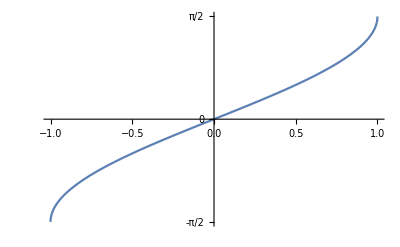

```mathematica
Plot[ArcSin[x],{x,-1,1},Ticks->{Automatic,{-π/2,0,π/2}}]
```

```mathematica
SCAFE[HoldForm@(Cos[ArcSin[x]]^2),ReleaseHold]
```

Cos[ArcSin[x]]^2==1-x^2

```mathematica
Cos[arcsin[x]]^2==1-x^2
SCMAF[%,(ⅆ#)/ⅆx&,All,Level->{1},Apply->SCEvalDeriv,
SCSolve,{All,arcsin'[x]},
RA,{At[2],arcsin[x]->ArcSin[x]}]
```

Cos[arcsin[x]]^2==1-x^2

arcsin'[x]==x Csc[arcsin[x]] Sec[arcsin[x]]

arcsin'[x]==1/(√(1-x^2))

```mathematica
SCAFE[ⅆArcSin[x]/ⅆx,SCEvalDeriv,All,Apply->Simplify]
```

ⅆArcSin[x]/ⅆx==1/(√(1-x^2))

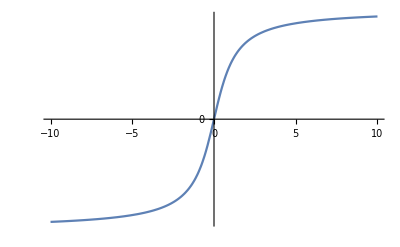

```mathematica
Plot[ArcTan[x],{x,-10,10},Ticks->{Automatic,{-π/2,0,π/2}}]
```

```mathematica
SCAFE[Underscript[Limit, x->∞][ArcTan[x]],SCEvalLimit]
```

Limit_(x→∞)[ArcTan[x]]==π/2

```mathematica
Tan[arctan[x]]==x
SCMAF[%,(ⅆ#)/ⅆx&,All,Level->{1},Apply->SCEvalDeriv,,
SCSolve,{All,arctan'[x]},
RA,{At[2],arctan->ArcTan}]
```

Tan[arctan[x]]==x

Sec[arctan[x]]^2 arctan'[x]==1

arctan'[x]==Cos[arctan[x]]^2

arctan'[x]==1/(1+x^2)

```mathematica
SCAFE[ⅆArcTan[x]/ⅆx,SCEvalDeriv]
```

ⅆArcTan[x]/ⅆx==1/(1+x^2)

Applying Your Knowledge

```mathematica
Cot[arccot[x]]==x
SCMAF[%,(ⅆ#)/ⅆx&,All,Level->{1},Apply->SCEvalDeriv,,
SCSolve,{All,arccot'[x]},
RA,{At[2],arccot->ArcCot},Apply->ExpandAll]
```

Cot[arccot[x]]==x

-Csc[arccot[x]]^2 arccot'[x]==1

arccot'[x]==-Sin[arccot[x]]^2

arccot'[x]==-1/(1+x^2)

```mathematica
SCAFE[ⅆArcCot[x]/ⅆx,SCEvalDeriv]
```

ⅆArcCot[x]/ⅆx==-1/(1+x^2)

```mathematica
Sec[arcsec[x]]==x
SCMAF[%,(ⅆ#)/ⅆx&,All,Level->{1},Apply->SCEvalDeriv,
SCSolve,{All,arcsec'[x]},
RA,{At[2],arcsec->ArcSec},
SCFactor,{1-1/x^2,1/x^2},
RR,{At[2],x^-2->Abs[x]^-2}]
```

Sec[arcsec[x]]==x

arcsec'[x]==1/(√((-1+x^2)/x^2) x^2)

arcsec'[x]==1/(√(-1+x^2) |x|)

```mathematica
SCAFE[ⅆArcSec[x]/ⅆx,SCEvalDeriv]
SCMAF[%,SCFactor,{1-1/x^2,1/x^2},
RR,{At[2],x^-2->Abs[x]^-2}]
```

ⅆArcSec[x]/ⅆx==1/(x^2 √(1-1/x^2))

ⅆArcSec[x]/ⅆx==1/(√((-1+x^2)/x^2) x^2)

ⅆArcSec[x]/ⅆx==1/(√(-1+x^2) |x|)

```mathematica
Csc[arccsc[x]]==x
SCMAF[%,(ⅆ#)/ⅆx&,All,Level->{1},Apply->SCEvalDeriv,
SCSolve,{All,arccsc'[x]},
RA,{At[2],arccsc->ArcCsc},
SCFactor,{1-1/x^2,1/x^2},
RR,{At[2],x^-2->Abs[x]^-2}]
```

Csc[arccsc[x]]==x

arccsc'[x]==-1/(√((-1+x^2)/x^2) x^2)

arccsc'[x]==-1/(√(-1+x^2) |x|)

```mathematica
SCAFE[ⅆArcCsc[x]/ⅆx,SCEvalDeriv]
SCMAF[%,SCFactor,{1-1/x^2,1/x^2},
RR,{At[2],x^-2->Abs[x]^-2}]
```

ⅆArcCsc[x]/ⅆx==-1/(x^2 √(1-1/x^2))

ⅆArcCsc[x]/ⅆx==-1/(√((-1+x^2)/x^2) x^2)

ⅆArcCsc[x]/ⅆx==-1/(√(-1+x^2) |x|)

Exercises

h.

```mathematica
SCARA[ⅆ/ⅆx ArcTan[ⅇ^(2x)],ⅆArcTan[f_]/ⅆx:> 1/(1+f^2)ⅆf/ⅆx,Apply->SCEvalDeriv]
```

ⅆArcTan[ⅇ^(2 x)]/ⅆx==(2 ⅇ^(2 x))/(1+ⅇ^(4 x))

```mathematica
SCAFE[ⅆ/ⅆx ArcTan[ⅇ^(2x)],SCEvalDeriv]
```

ⅆArcTan[ⅇ^(2 x)]/ⅆx==(2 ⅇ^(2 x))/(1+ⅇ^(4 x))

i.

```mathematica
SCAFE[∫1/(1+x^2)ⅆx,SCTransInt,{All,TransVar->{x,u,x==Tan[u]}},Apply->Simplify]
SCMAF[%,SCEvalInt,{At[2],ReplConst->C},
SCEliminate,{At[2],x==Tan[u],u},
Refine,{All,C[1]==0}]
```

∫1/(1+x^2)ⅆx==∫1ⅆu

ConditionalExpression[∫1/(1+x^2)ⅆx==C+ArcTan[x]+π C[1],C[1]∈ℤ]

∫1/(1+x^2)ⅆx==C+ArcTan[x]

```mathematica
SCAFE[∫1/(1+x^2)ⅆx,SCEvalInt,{All,ReplConst->C}]
```

∫1/(1+x^2)ⅆx==C+ArcTan[x]

j.

```mathematica
SCAFE[∫1/(√(1-16 x^2))ⅆx,SCTransInt,{All,TransVar->{x,u,4x==u}}]
SCMAF[%,RA,{At[2],∫1/(√(1-u^2))ⅆu==ArcSin[u]+4C},Apply->ExpandAll]
```

∫1/(√(1-16 x^2))ⅆx==1/4 ∫1/(√(1-u^2))ⅆu

∫1/(√(1-16 x^2))ⅆx==C+ArcSin[u]/4

```mathematica
SCAFE[∫1/(√(1-16 x^2))ⅆx,SCEvalInt,{All,ReplConst->C}]
```

∫1/(√(1-16 x^2))ⅆx==C+1/4 ArcSin[4 x]

k.

```mathematica
SCAFE[∫x/(x^2+9)ⅆx,SCTransInt,{All,TransVar->{x,u,x/3==u}}]
SCMAF[%,Factor,{9+9 u^2},
RA,{At[2],∫u/(1+u^2)ⅆu==1/2 Log[1+u^2]+c}]
```

∫x/(9+x^2)ⅆx==9 ∫u/(9+9 u^2)ⅆu

∫x/(9+x^2)ⅆx==∫u/(1+u^2)ⅆu

∫x/(9+x^2)ⅆx==c+1/2 Log[1+u^2]

```mathematica
SCAFE[∫x/(x^2+9)ⅆx,SCEvalInt,{All,ReplConst->C}]
```

∫x/(9+x^2)ⅆx==C+1/2 Log[9+x^2]

#### Trigonometric Substitution

```mathematica
SCAFE[∫1/(√(4-x^2))ⅆx,SCTransInt,{All,TransVar->{x,u,x==2Cos[u]}},Apply->Simplify]
SCMAF[%,FullSimplify,{At[2],Assumptions->{u∈Reals}},
SCEvalInt,{At[2],ReplConst->-C,Assumptions->u∈Reals},
SCEliminate,{All,x==2Cos[u],u},
Refine,{All,{C[1]==0,-2≤x≤2}},Part->{2}]
```

∫1/(√(4-x^2))ⅆx==-∫Csc[u] √(Sin[u]^2)ⅆu

{{ConditionalExpression[∫1/(√(4-x^2))ⅆx==C-(Piecewise[{{ArcCos[x/2]-2 π C[1], -Sin[ArcCos[x/2]-2 π C[1]]<0}, {-ArcCos[x/2]+2 π C[1], True}}]),C[1]∈ℤ]},{ConditionalExpression[∫1/(√(4-x^2))ⅆx==C-(Piecewise[{{-ArcCos[x/2]-2 π C[1], Sin[ArcCos[x/2]+2 π C[1]]<0}, {ArcCos[x/2]+2 π C[1], True}}]),C[1]∈ℤ]}}

∫1/(√(4-x^2))ⅆx==C-ArcCos[x/2]

```mathematica
SCAFE[∫1/(√(4-x^2))ⅆx,SCEvalInt,{All,ReplConst->C}]
```

∫1/(√(4-x^2))ⅆx==C+ArcSin[x/2]

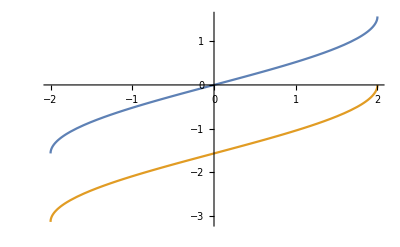

```mathematica
Plot[{ArcSin[x/2],-ArcCos[x/2]},{x,-2,2}]
```

```mathematica
SCAFE[∫x/(√(9+x^2))ⅆx,SCTransInt,{All,TransVar->{x,u,x^2+9==u}}]
SCMAF[%,SCEvalInt,{At[2],ReplConst->2C},
RA,{At[2],Reverse[x^2+9==u]},Apply->Expand]
```

∫x/(√(9+x^2))ⅆx==1/2 ∫1/(√u)ⅆu

∫x/(√(9+x^2))ⅆx==1/2 (2 C+2 √u)

∫x/(√(9+x^2))ⅆx==C+√(9+x^2)

```mathematica
SCAFE[∫x/(√(9+x^2))ⅆx,SCEvalInt,{All,ReplConst->C}]
```

∫x/(√(9+x^2))ⅆx==C+√(9+x^2)

## Lab 27: Partial Fractions

Introduction

```mathematica
SCAFE[∫(2x+3)/(x^2-5x+4)ⅆx,Apart,(2x+3)/(x^2-5x+4),ApplyAll->SCExpandInt]
SCMAF[%,SCTransInt,{{∫1/(-4+x)ⅆx,TransVar->{x,u,-4+x==u}},{∫1/(-1+x)ⅆx,TransVar->{x,v,-1+x==v}}},
SCEvalInt,{At[2],ReplConst->C},
RA,{At[2],{u==x-4,v==x-1}},Apply->ExpandAll,
RA,{At[2],(11 C)/3-(5 C[2])/3->C}]
```

∫(3+2 x)/(4-5 x+x^2)ⅆx==11/3 ∫1/(-4+x)ⅆx-5/3 ∫1/(-1+x)ⅆx

∫(3+2 x)/(4-5 x+x^2)ⅆx==(11 C)/3-(5 C[2])/3+11/3 Log[-4+x]-5/3 Log[-1+x]

∫(3+2 x)/(4-5 x+x^2)ⅆx==C+11/3 Log[-4+x]-5/3 Log[-1+x]

```mathematica
SCAFE[∫(2x+3)/(x^2-5x+4)ⅆx,SCEvalInt,{All,ReplConst->C}]
```

∫(3+2 x)/(4-5 x+x^2)ⅆx==C-5/3 Log[1-x]+11/3 Log[4-x]

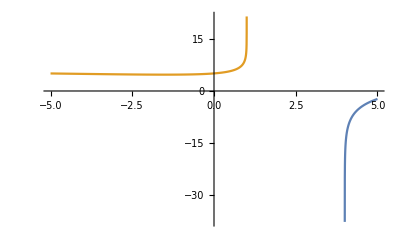

```mathematica
Plot[{11/3 Log[-4+x]-5/3 Log[-1+x],-5/3 Log[1-x]+11/3 Log[4-x]},{x,-5,5},PlotRange->All]
```

What is wrong? 
Answer: https://mathematica.stackexchange.com/questions/22705/simplify-expressions-with-log

```mathematica
SCAFE[∫(2x+3)/(x^2-5x+4)ⅆx,Apart,(2x+3)/(x^2-5x+4),ApplyAll->SCExpandInt]
SCMAF[%,SCTransInt,{{∫1/(-4+x)ⅆx,TransVar->{x,u,-4+x==u}},{∫1/(-1+x)ⅆx,TransVar->{x,v,-1+x==v}}},
SCEvalInt,{At[2],ReplConst->C},
RA,{At[2],{u==x-4,v==x-1}},Apply->ExpandAll,
ComplexExpand,At[2],
RR,{At[2],{(11 C)/3-(5 C[2])/3->C,Arg[x_]->0}}]
```

∫(3+2 x)/(4-5 x+x^2)ⅆx==11/3 ∫1/(-4+x)ⅆx-5/3 ∫1/(-1+x)ⅆx

∫(3+2 x)/(4-5 x+x^2)ⅆx==(11 C)/3+ⅈ (11/3 Arg[-4+x]-5/3 Arg[-1+x])-(5 C[2])/3+11/6 Log[(-4+x)^2]-5/6 Log[(-1+x)^2]

∫(3+2 x)/(4-5 x+x^2)ⅆx==C+11/6 Log[(-4+x)^2]-5/6 Log[(-1+x)^2]

Exercise:

a.

```mathematica
SCAFE[∫(4x-3)/(2 x^3-3 x^2+x)ⅆx,Apart,{(4x-3)/(2 x^3-3 x^2+x)},ApplyAll->SCExpandInt]
SCMAF[%,SCEvalInt,{At[2],ReplConst->C},Apply->ExpandAll,
ComplexExpand,At[2],
RR,{At[2],{Arg[x_]->0,C-3 C[2]+4 C[3]->C,Log[x_^2]->Log[Abs[x]^2]}},
Apply->Simplify]
```

∫(-3+4 x)/(x-3 x^2+2 x^3)ⅆx==∫1/(-1+x)ⅆx-3 ∫1/x ⅆx+4 ∫1/(-1+2 x)ⅆx

∫(-3+4 x)/(x-3 x^2+2 x^3)ⅆx==C+ⅈ (Arg[-1+x]-3 Arg[x]+2 Arg[-1+2 x])-3 C[2]+4 C[3]+1/2 Log[(-1+x)^2]-(3 Log[x^2])/2+Log[(-1+2 x)^2]

∫(-3+4 x)/(x-3 x^2+2 x^3)ⅆx==C+2 Log[|1-2 x|]+Log[|-1+x|]-3 Log[|x|]

```mathematica
SCAFE[∫(4x-3)/(2 x^3-3 x^2+x)ⅆx,SCEvalInt,{All,ReplConst->C},Apply->ComplexExpand]
SCMAF[%,RA,{At[2],{Arg[x_]->0,Log[x_^2]->Log[Abs[x]^2]}},
Apply->Simplify]
```

∫(-3+4 x)/(x-3 x^2+2 x^3)ⅆx==C+ⅈ (2 Arg[1-2 x]+Arg[1-x]-3 Arg[x])+Log[(1-2 x)^2]+1/2 Log[(1-x)^2]-(3 Log[x^2])/2

∫(-3+4 x)/(x-3 x^2+2 x^3)ⅆx==C+2 Log[|1-2 x|]+Log[|1-x|]-3 Log[|x|]

b.

```mathematica
SCAFE[∫(3 x^2-1)/(x^3-4x)ⅆx,Apart,{(3 x^2-1)/(x^3-4x)},ApplyAll->SCExpandInt]
SCMAF[%,SCEvalInt,{At[2],ReplConst->C},Apply->ExpandAll,
ComplexExpand,At[2],
RR,{At[2],{Arg[x_]->0,(11 C)/8+C[2]/4+(11 C[3])/8->C,Log[x_^2]->Log[Abs[x]^2]}},
Apply->Simplify]
```

∫(-1+3 x^2)/(-4 x+x^3)ⅆx==11/8 ∫1/(-2+x)ⅆx+1/4 ∫1/x ⅆx+11/8 ∫1/(2+x)ⅆx

∫(-1+3 x^2)/(-4 x+x^3)ⅆx==(11 C)/8+ⅈ (11/8 Arg[-2+x]+Arg[x]/4+11/8 Arg[2+x])+C[2]/4+(11 C[3])/8+11/16 Log[(-2+x)^2]+Log[x^2]/8+11/16 Log[(2+x)^2]

∫(-1+3 x^2)/(-4 x+x^3)ⅆx==1/8 (8 C+11 Log[|-2+x|]+2 Log[|x|]+11 Log[|2+x|])

```mathematica
SCAFE[∫(3 x^2-1)/(x^3-4x)ⅆx,SCEvalInt,{All,ReplConst->C},Apply->ComplexExpand]
SCMAF[%,RA,{At[2],{Arg[x_]->0,Log[x_^2]->Log[Abs[x]^2]}},
Apply->Simplify]
```

∫(-1+3 x^2)/(-4 x+x^3)ⅆx==C+ⅈ (Arg[x]/4+11/8 Arg[4-x^2])+Log[x^2]/8+11/16 Log[(4-x^2)^2]

∫(-1+3 x^2)/(-4 x+x^3)ⅆx==C+1/4 Log[|x|]+11/8 Log[|4-x^2|]

Demonstration: Find the Coefficients of a Partial Fraction Decomposition

```mathematica
(4x-2)/(x^3-4 x^2+4x)==A/x+B/(x-2)+C/(x-2)^2
SCMAF[%,SCMultEq,{All,x^3-4 x^2+4x},Apply->Simplify,
{#,(∂#)/(∂x),(∂^2 #)/(∂x^2)}&,All,
Thread,{All,Equal},Level->{1},Apply->SCEvalDeriv,
RA,{All,x->0},
SCSolve,{All,{A,B,C}}]
```

(-2+4 x)/(4 x-4 x^2+x^3)==C/(-2+x)^2+B/(-2+x)+A/x

{0==2+4 A,4==-4 A-2 B+C,0==2 A+2 B}

{A==-1/2,B==1/2,C==3}

```mathematica
(4x-2)/(x^3-4 x^2+4x)==A/x+B/(x-2)+C/(x-2)^2
SCMAF[%,RA,{All,{A==-1/2,B==1/2,C==3}},Apply->Simplify]
```

(-2+4 x)/(4 x-4 x^2+x^3)==C/(-2+x)^2+B/(-2+x)+A/x

True

## Project Set 3

### Project 1: Estimating Area

a.

f[x]==1+7 x^2-x^3

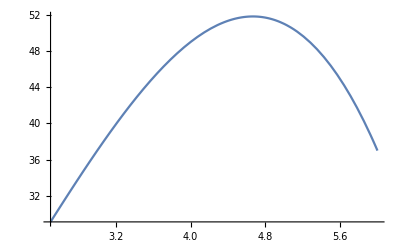

```mathematica
f[x]==-x^3+7 x^2+1
SCMAF[%,Plot,{At[2],{x,2.5,6}},Part->{2}]
```

```mathematica
SCARA[ⅆ/ⅆx f[x],f[x]==-x^3+7 x^2+1,Apply->SCEvalDeriv]
SCMAF[%,RA,{At[1],ⅆf[x]/ⅆx==0},
SCSolve,{All,x}]
```

ⅆf[x]/ⅆx==14 x-3 x^2

0==14 x-3 x^2

{{x==0},{x==14/3}}

The minimum and maximum values are

```mathematica
SCARA[f[25/10],f->Function[{x},-x^3+7 x^2+1]]
```

f[5/2]==233/8

```mathematica
SCARA[f[14/3],f->Function[{x},-x^3+7 x^2+1]]
```

f[14/3]==1399/27

b.

f[x]==1+7 x^2-x^3

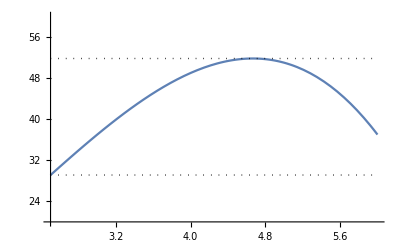

```mathematica
f[x]==-x^3+7 x^2+1
SCMAF[%,Plot,{At[2],{x,2.5,6},PlotRange->{20,60},Epilog->{Dotted,Line[{{2.5,1399/27},{6,1399/27}}],Line[{{2.5,233/8},{6,233/8}}]}},Part->{2}]
```

g.

```mathematica
SCARA[∫_(25/10)^6 f[x]ⅆx,f[x]==-x^3+7 x^2+1,Apply->SCEvalInt]
```

∫_(5/2)^6 f[x]ⅆx==30107/192

Using the fundamental theorem of calculus and antiderivative,

```mathematica
SCARA[∫f[x]ⅆx,f[x]==-x^3+7 x^2+1,Apply->SCEvalInt]
```

∫f[x]ⅆx==x+(7 x^3)/3-x^4/4

```mathematica
∫_(25/10)^6 f[x]ⅆx==Subscript[(x+(7 x^3)/3-x^4/4), x==6]-Subscript[(x+(7 x^3)/3-x^4/4), x==25/10]
SCMAF[%,SCEvalEqSub,At[2]]
```

∫_(5/2)^6 f[x]ⅆx==-(x+(7 x^3)/3-x^4/4)_(x==5/2)+(x+(7 x^3)/3-x^4/4)_(x==6)

∫_(5/2)^6 f[x]ⅆx==30107/192

### Project 2: A Snow-Filled Year

a.

```mathematica
"distance"=="speed" "time"
SCMAF[%,RA,{At[2],{"speed"->Quantity[60, ("Miles")/("Hours")],"time"->Quantity[3, "Hours"]}}]
```

distance==speed time

distance==180 mi

b.

```mathematica
distance==∫_0^30 f[t]ⅆt
SCMAF[%,RA,{At[2],f[t]==(10t)/(t+2)}]
SCMAF[%,SCEvalInt,At[2],Apply->N]
```

distance==∫_0^30 f[t]ⅆt

distance==10 ∫_0^30 t/(2+t)ⅆt

distance==244.548

With units

```mathematica
distance==∫_(0Quantity[, "Seconds"])^(30Quantity[, "Seconds"]) f[t]ⅆt
SCMAF[%,RA,{At[2],f[t]==(10t)/(t+2 Quantity[, "Seconds"])Quantity[, ("Feet")/("Seconds")]},Apply->SCEvalInt]
```

distance==∫_(0 s)^(30 s) f[t]ⅆt

distance==-10 (-30+Log[256]) ft

c.

```mathematica
S[1]==∫_0^1 s[t]ⅆt
SCMAF[%,RA,{At[2],s[t]==8.2-0.7t-0.6 t^2},Apply->SCEvalInt]
```

S[1]==∫_0^1 s[t]ⅆt

S[1]==7.65

7.65 inches of snow fell in January.

d.

```mathematica
S[1]==∫_1^2 s[t]ⅆt
SCMAF[%,RA,{At[2],s[t]==8.2-0.7t-0.6 t^2},Apply->SCEvalInt]
```

S[1]==∫_1^2 s[t]ⅆt

S[1]==5.75

5.75 inches of snow fell in February.

e.

We needs the average rate of snowfall in December.

### Project 3: Trapezoidal and Simpson’s Rule

a.

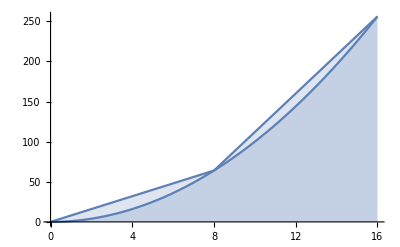

```mathematica
Show[Plot[x^2,{x,0,16},Filling->Axis],ListLinePlot[Table[{x,x^2},{x,0,16,8}],Filling->Axis]]
```

```mathematica
S==Subscript[S, 1]+Subscript[S, 2]
SCMAF[%,RA,{At[2],{Subscript[S, 1]==(0^2+8^2)/2 8,Subscript[S, 2]==(8^2+16^2)/2 8}}]
```

S==S_1+S_2

S==1536

b.

With 4 trapezoids,

```mathematica
Block[{dx=16/4},Total@Table[(x^2+(x+dx)^2)/2 dx,{x,0,16-dx,dx}]]
```

1408

With 8 trapezoids,

```mathematica
Block[{dx=16/8},Total@Table[(x^2+(x+dx)^2)/2 dx,{x,0,16-dx,dx}]]
```

1376

With 16 trapezoids,

```mathematica
Block[{dx=16/16},Total@Table[(x^2+(x+dx)^2)/2 dx,{x,0,16-dx,dx}]]
```

1368

c.

With 2 trapezoids,

```mathematica
Block[{dx=(π/2)/2},N@Total@Table[(Cos[x]+Cos[x+dx])/2 dx,{x,0,π/2-dx,dx}]]
```

0.948059

With 4 trapezoids,

```mathematica
Block[{dx=(π/2)/4},N@Total@Table[(Cos[x]+Cos[x+dx])/2 dx,{x,0,π/2-dx,dx}]]
```

0.987116

With 8 trapezoids,

```mathematica
Block[{dx=(π/2)/8},N@Total@Table[(Cos[x]+Cos[x+dx])/2 dx,{x,0,π/2-dx,dx}]]
```

0.996785

With 16 trapezoids,

```mathematica
Block[{dx=(π/2)/16},N@Total@Table[(Cos[x]+Cos[x+dx])/2 dx,{x,0,π/2-dx,dx}]]
```

0.999197

```mathematica
∫_0^(π/2) Cos[x]ⅆx//SCEvalInt
```

1

d.

```mathematica
∫_a^b f[x]ⅆx==∑_(j=0)^(n-1) (f[Subscript[x, n]]+f[Subscript[x, n+1]])/2 Δx
```

∫_a^b f[x]ⅆx==∑_(j=0)^(-1+n) 1/2 Δx (f[x_n]+f[x_(1+n)])

where n is the number of subintervals and Δx is the width of each subinterval.

e.

Composite Simpson's rule

```mathematica
∫_a^b f[x]ⅆx==h/3(f[Subscript[x, 0]]+2∑_(j=1)^(n/2-1) f[Subscript[x, 2j]]+4∑_(j=1)^(n/2) f[Subscript[x, 2j-1]]+f[Subscript[x, n]])
SCMAF[%,RA,{All,{a==0,b==π/2,n==2,f==Cos}},Apply->SCEvalSum,
RR,{At[2],{Subscript[x, j_]->0+j h,h==1/n π/2,n==2}},Apply->N]
```

∫_a^b f[x]ⅆx==h/3 (f[x_0]+f[x_n]+2 ∑_(j=1)^(-1+n/2) f[x_(2 j)]+4 ∑_(j=1)^(n/2) f[x_(-1+2 j)])

∫_0^(π/2) Cos[x]ⅆx==1/3 h (Cos[x_0]+4 Cos[x_1]+Cos[x_2])

∫_0^(π/2) Cos[x]ⅆx==1.00228

```mathematica
∫_a^b f[x]ⅆx==h/3(f[Subscript[x, 0]]+2∑_(j=1)^(n/2-1) f[Subscript[x, 2j]]+4∑_(j=1)^(n/2) f[Subscript[x, 2j-1]]+f[Subscript[x, n]])
SCMAF[%,RA,{All,{a==0,b==π/2,n==4,f==Cos}},Apply->SCEvalSum,
RR,{At[2],{Subscript[x, j_]->0+j h,h==1/n π/2,n==4}},Apply->N]
```

∫_a^b f[x]ⅆx==h/3 (f[x_0]+f[x_n]+2 ∑_(j=1)^(-1+n/2) f[x_(2 j)]+4 ∑_(j=1)^(n/2) f[x_(-1+2 j)])

∫_0^(π/2) Cos[x]ⅆx==1/3 h (Cos[x_0]+2 Cos[x_2]+4 (Cos[x_1]+Cos[x_3])+Cos[x_4])

∫_0^(π/2) Cos[x]ⅆx==1.00013

```mathematica
∫_a^b f[x]ⅆx==h/3(f[Subscript[x, 0]]+2∑_(j=1)^(n/2-1) f[Subscript[x, 2j]]+4∑_(j=1)^(n/2) f[Subscript[x, 2j-1]]+f[Subscript[x, n]])
SCMAF[%,RA,{All,{a==0,b==π/2,n==8,f==Cos}},Apply->SCEvalSum,
RR,{At[2],{Subscript[x, j_]->0+j h,h==1/n π/2,n==8}},Apply->N]
```

∫_a^b f[x]ⅆx==h/3 (f[x_0]+f[x_n]+2 ∑_(j=1)^(-1+n/2) f[x_(2 j)]+4 ∑_(j=1)^(n/2) f[x_(-1+2 j)])

∫_0^(π/2) Cos[x]ⅆx==1/3 h (Cos[x_0]+2 (Cos[x_2]+Cos[x_4]+Cos[x_6])+4 (Cos[x_1]+Cos[x_3]+Cos[x_5]+Cos[x_7])+Cos[x_8])

∫_0^(π/2) Cos[x]ⅆx==1.00001

### Project 4: Applying Area Between Curves

a.

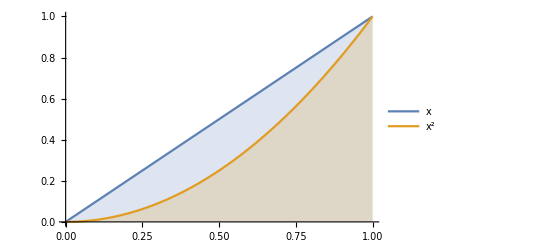

```mathematica
Plot[{x,x^2},{x,0,1},Filling->Axis,PlotLegends->"Expressions"]
```

```mathematica
SCAFE[∫_0^1 (x-x^2)ⅆx,SCEvalInt]
```

∫_0^1 (x-x^2)ⅆx==1/6

b.

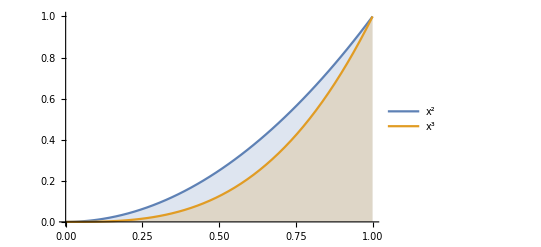

```mathematica
Plot[{x^2,x^3},{x,0,1},Filling->Axis,PlotLegends->"Expressions"]
```

```mathematica
SCAFE[∫_0^1 (x^2-x^3)ⅆx,SCEvalInt]
```

∫_0^1 (x^2-x^3)ⅆx==1/12

c.

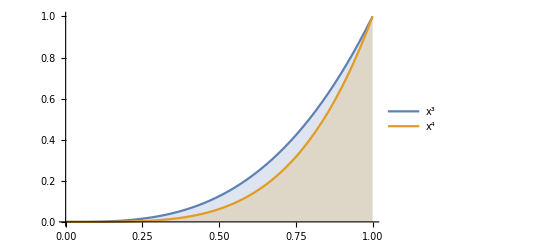

```mathematica
Plot[{x^3,x^4},{x,0,1},Filling->Axis,PlotLegends->"Expressions"]
```

```mathematica
SCAFE[∫_0^1 (x^3-x^4)ⅆx,SCEvalInt]
```

∫_0^1 (x^3-x^4)ⅆx==1/20

d.

```mathematica
SCAFE[∫_0^1 (x^n-x^(n+1))ⅆx,SCEvalInt]
SCMAF[%,Refine,{All,n>0},Apply->Factor]
```

ConditionalExpression[∫_0^1 (x^n-x^(1+n))ⅆx==1/(2+3 n+n^2),Re[n]>-1]

∫_0^1 (x^n-x^(1+n))ⅆx==1/((1+n) (2+n))

e.

```mathematica
Subscript[F, n]==1/((1+n) (2+n));
```

f, g.

```mathematica
Table[Subscript[S, n]==∑_(i=1)^n Subscript[F, i]/.n->j,{j,1,10}]
SCMAF[%,SCEvalSum,All,
RA,{All,Subscript[F, i_]==1/((1+i) (2+i))},
Thread,{All,Equal}]
```

{S_1==∑_(i=1)^1 F_i,S_2==∑_(i=1)^2 F_i,S_3==∑_(i=1)^3 F_i,S_4==∑_(i=1)^4 F_i,S_5==∑_(i=1)^5 F_i,S_6==∑_(i=1)^6 F_i,S_7==∑_(i=1)^7 F_i,S_8==∑_(i=1)^8 F_i,S_9==∑_(i=1)^9 F_i,S_10==∑_(i=1)^10 F_i}

{S_1==1/6,S_2==1/4,S_3==3/10,S_4==1/3,S_5==5/14,S_6==3/8,S_7==7/18,S_8==2/5,S_9==9/22,S_10==5/12}

{S_1,S_2,S_3,S_4,S_5,S_6,S_7,S_8,S_9,S_10}=={1/6,1/4,3/10,1/3,5/14,3/8,7/18,2/5,9/22,5/12}

```mathematica
FindSequenceFunction[{1/6,1/4,3/10,1/3,5/14,3/8,7/18,2/5,9/22,5/12},n]
```

n/(2 (2+n))

Using MathSymbolica,

```mathematica
Subscript[S, n]==∑_(i=1)^n Subscript[F, i]
SCMAF[%,RA,{At[2],Subscript[F, n_]==1/((1+n) (2+n))},Apply->SCEvalSum]
SCMAF[%,Factor,At[2]]
```

S_n==∑_(i=1)^n F_i

S_n==1/2-1/(2+n)

S_n==n/(2 (2+n))

### Project 5: Surface Area with Parallelograms

Demonstration: Finding the Area of a 3D Surface with Parallelograms

a, b.

```mathematica
Show[Plot3D[x^2+y^2,{x,-1,1},{y,-1,1},AxesLabel->Automatic,PlotStyle->Opacity[0.5]],
Graphics3D[{Opacity[0.8],
Flatten@Table[Polygon[{{x,y,f[x,y]},{x+Δ,y,f[x+Δ,y]},{x+Δ,y+Δ,f[x+Δ,y+Δ]},{x,y+Δ,f[x,y+Δ]}}],{x,-1,1-1,1},{y,-1,1-1,1}]
}//.{Δ->1,f[x_,y_]->x^2+y^2}]]
```

-Graphics3D-

c.

```mathematica
S==4Area[Polygon[{{-1,-1,f[-1,-1]},{-1,0,f[-1,0]},{0,0,f[0,0]},{0,-1,f[0,-1]}}]/.f[x_,y_]->x^2+y^2]
```

S==4 √3

```mathematica
S==4Norm[({Subscript[x, i]+Δ,Subscript[y, j],f[Subscript[x, i]++Δ,Subscript[y, j]]}-{Subscript[x, i],Subscript[y, j],f[Subscript[x, i],Subscript[y, j]]})×({Subscript[x, i],Subscript[y, j]+Δ,f[Subscript[x, i],Subscript[y, j]+Δ]}-{Subscript[x, i],Subscript[y, j],f[Subscript[x, i],Subscript[y, j]]})]
SCMAF[%,RR,{At[2],{Subscript[x, i]->-1,Subscript[y, j]->-1,Δ->1,f[x_,y_]->x^2+y^2}},Apply->N]
```

S==4 √((|Δ|)^4+(|Δ f[x_i,y_j]-Δ f[x_i,Δ+y_j]|)^2+(|Δ f[x_i,y_j]-Δ f[Δ+x_i,y_j]|)^2)

S==6.9282

d.

```mathematica
S==∑_(j=0)^n ∑_(i=0)^n Norm[({Subscript[x, i]+Δ,Subscript[y, j],f[Subscript[x, i]++Δ,Subscript[y, j]]}-{Subscript[x, i],Subscript[y, j],f[Subscript[x, i],Subscript[y, j]]})×({Subscript[x, i],Subscript[y, j]+Δ,f[Subscript[x, i],Subscript[y, j]+Δ]}-{Subscript[x, i],Subscript[y, j],f[Subscript[x, i],Subscript[y, j]]})]
SCMAF[%,RA,{At[2],{Subscript[x, i]->Subscript[x, 0]+i Δ,Subscript[y, j]->Subscript[y, 0]+j Δ}},
RR,{At[2],{n==9,Δ==2/10,Subscript[x, 0]==-1,Subscript[y, 0]==-1,f[x_,y_]->x^2+y^2}},
SCEvalSum,At[2],Apply->N]
```

S==∑_(j=0)^n ∑_(i=0)^n √((|Δ|)^4+(|Δ f[x_i,y_j]-Δ f[x_i,Δ+y_j]|)^2+(|Δ f[x_i,y_j]-Δ f[Δ+x_i,y_j]|)^2)

S==∑_(j=0)^9 ∑_(i=0)^9 √(1/625+(|1/5 (-(-4/5+i/5)^2-(-1+j/5)^2)+1/5 ((-1+i/5)^2+(-1+j/5)^2)|)^2+(|1/5 ((-1+i/5)^2+(-1+j/5)^2)+1/5 (-(-1+i/5)^2-(-4/5+j/5)^2)|)^2)

S==7.42478

g.

```mathematica
S==∑_(j=0)^n ∑_(i=0)^n Norm[({Subscript[x, i]+Δ,Subscript[y, j],f[Subscript[x, i]++Δ,Subscript[y, j]]}-{Subscript[x, i],Subscript[y, j],f[Subscript[x, i],Subscript[y, j]]})×({Subscript[x, i],Subscript[y, j]+Δ,f[Subscript[x, i],Subscript[y, j]+Δ]}-{Subscript[x, i],Subscript[y, j],f[Subscript[x, i],Subscript[y, j]]})]
SCMAF[%,RA,{At[2],{Subscript[x, i]->Subscript[x, 0]+i Δ,Subscript[y, j]->Subscript[y, 0]+j Δ}},
Simplify,{At[2],Δ>0},
SCFactor,{(Δ^2+(|f[i Δ+Subscript[x, 0],j Δ+Subscript[y, 0]]-f[i Δ+Subscript[x, 0],Δ+j Δ+Subscript[y, 0]]|)^2+(|f[i Δ+Subscript[x, 0],j Δ+Subscript[y, 0]]-f[Δ+i Δ+Subscript[x, 0],j Δ+Subscript[y, 0]]|)^2),Δ^2},ApplyAll->PowerExpand]
```

S==∑_(j=0)^n ∑_(i=0)^n √((|Δ|)^4+(|Δ f[x_i,y_j]-Δ f[x_i,Δ+y_j]|)^2+(|Δ f[x_i,y_j]-Δ f[Δ+x_i,y_j]|)^2)

S==∑_(j=0)^n ∑_(i=0)^n Δ √(Δ^2+(|f[i Δ+x_0,j Δ+y_0]-f[i Δ+x_0,Δ+j Δ+y_0]|)^2+(|f[i Δ+x_0,j Δ+y_0]-f[Δ+i Δ+x_0,j Δ+y_0]|)^2)

S==∑_(j=0)^n ∑_(i=0)^n Δ^2 √(1+(|f[i Δ+x_0,j Δ+y_0]-f[i Δ+x_0,Δ+j Δ+y_0]|)^2/Δ^2+(|f[i Δ+x_0,j Δ+y_0]-f[Δ+i Δ+x_0,j Δ+y_0]|)^2/Δ^2)

```mathematica
S==∫_-1^1 ∫_-1^1 √(1+((∂f)/(∂x))^2+((∂f)/(∂y))^2)ⅆxⅆy
SCMAF[%,RA,{At[2],f==x^2+y^2},Apply->SCEvalDeriv,
SCEvalInt,At[2],Apply->N]
```

S==∫_-1^1 ∫_-1^1 √(1+((∂f)/(∂x))^2+((∂f)/(∂y))^2)ⅆxⅆy

S==∫_-1^1 ∫_-1^1 √(1+4 x^2+4 y^2)ⅆxⅆy

S==7.44626

### Project 6: Center of Mass and Biomechanics

a.

The top line segments

```mathematica
({0,1}+{-1.75,-.25})/2
```

{-0.875,0.375}

```mathematica
({0,1}+{1.75,-.25})/2
```

{0.875,0.375}

The lower segments

```mathematica
({-2,-.75}+{-1.75,-.25})/2
```

{-1.875,-0.5}

```mathematica
({2,-.75}+{1.75,-.25})/2
```

{1.875,-0.5}

The horizontal line segments

```mathematica
({0,-.25}+{-1.75,-.25})/2
```

{-0.875,-0.25}

```mathematica
({0,-.25}+{1.75,-.25})/2
```

{0.875,-0.25}

b.

```mathematica
1/100(24{-0.875,0.375}+24{0.875,0.375}+20{-1.875,-0.5}+20{1.875,-0.5}+6{-0.875,-0.25}+6{0.875,-0.1005})
```

{0.,-0.04103}